FittedModel[105.16+1.10962^(92.208-3.53219 x)]

105.16+1.10962^(92.208-3.53219 x)

0.994024

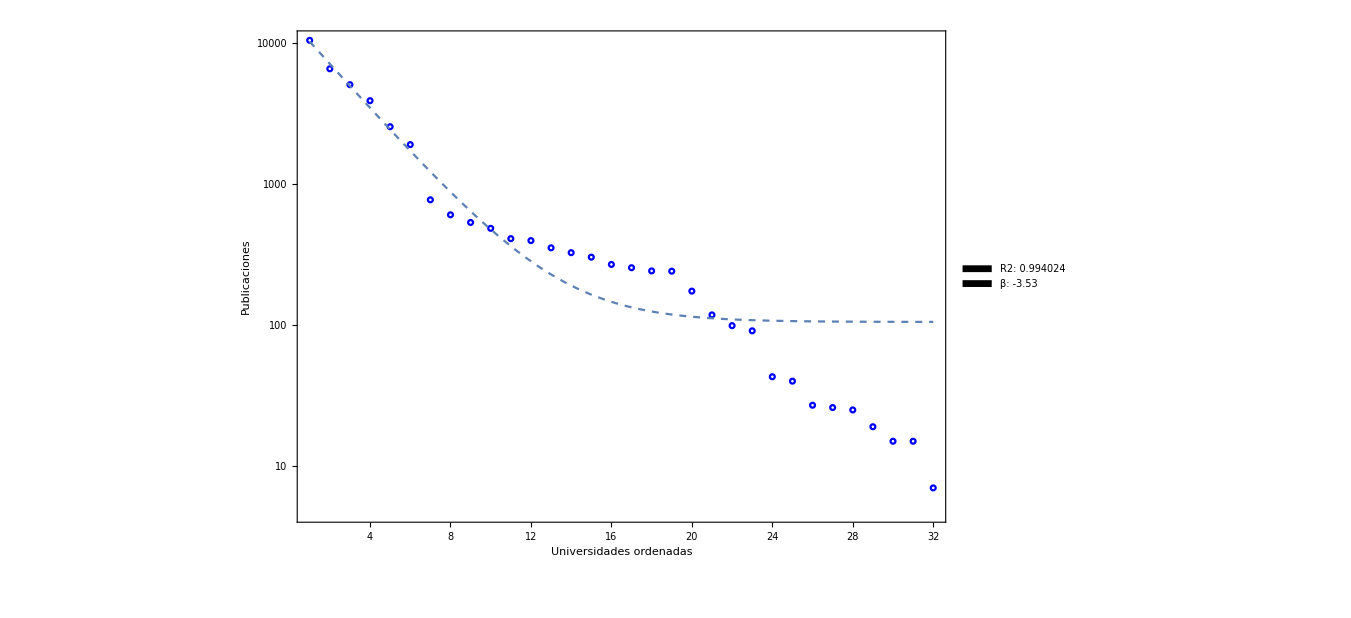

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados";
SetDirectory["/home/fabianact/ActualTesis/Tesis/ModelosPresentados/Distribución"];
SetOptions[ListLogPlot,BaseStyle->{FontSize->20}];
data1 = Import[y<>"/Distribución/Colombia.csv"];
Fdata1 = Flatten[data1];
lm1=NonlinearModelFit[Flatten[data1],(a) ^ (  (b x) + d )+ (c),{a,b, c, d},x]
P1=lm1["BestFit"] 
R21=lm1["AdjustedRSquared"] // ToString
Legended[Show[ListLogPlot[{Fdata1}, PlotRange->All, PlotStyle->{Blue},PlotMarkers->{Graphics[{Circle[]},ImageSize-> 5]}],LogPlot[lm1[x],{x,1,32}, PlotStyle->{Dashed}], AxesLabel->{"Universidades ordenadas", "Publicaciones"},ImageSize->1000, Frame->True,FrameLabel->{Style["Universidades ordenadas",Black,Large],Style["Publicaciones",Black,Large]}], Placed[SwatchLegend[{Black,Black},{Style["R2: "<>R21,15], Style["β: -3.53",15]},LegendMargins->{{0,0},{0,0}},LabelStyle->(FontFamily->"Helvetica")],{{0.60,0.6},{0,0}}]]
```

FittedModel[-13454.2+1.8011^(22.3566-1.02651 x)]

{-13454.2+1.8011^(22.3566-1.02651 x)}

0.846551

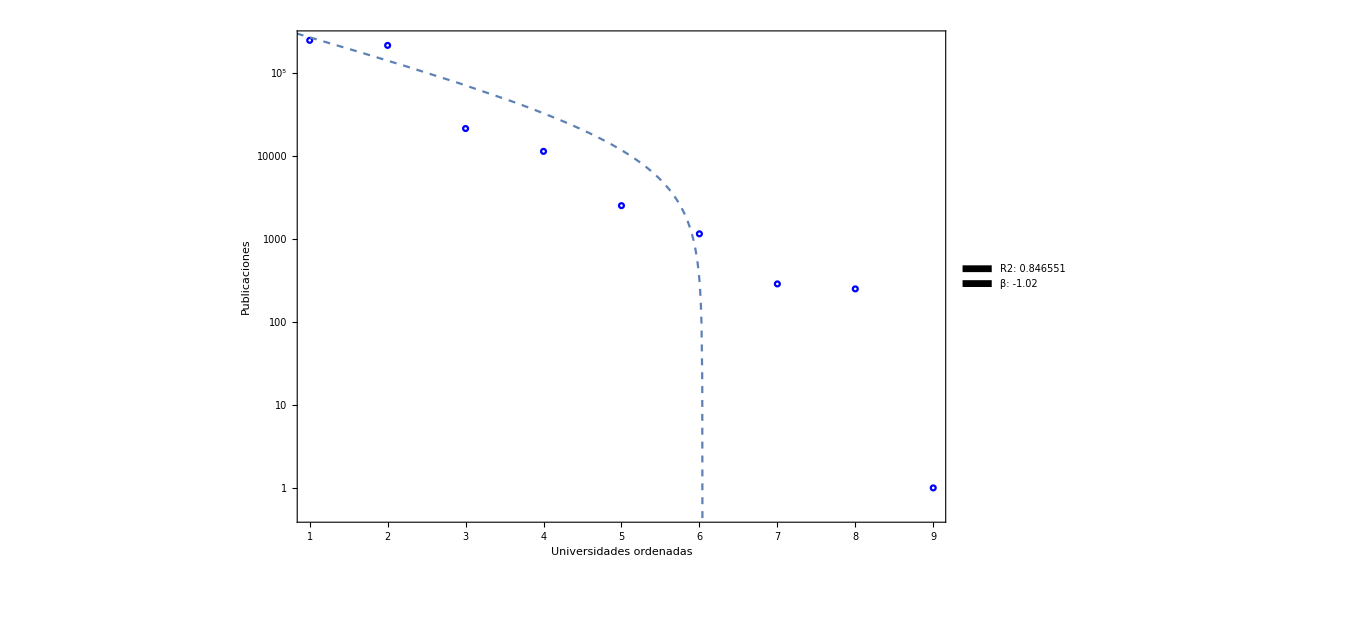

```mathematica
data1 = Import[y<>"/SinCompetencia/averageResults/dataUniversity-0.01-turtles.csv"];
Fdata1 = Flatten[data1];
lm1=NonlinearModelFit[Flatten[data1],(a) ^ (  (b x) + d )+ (c),{a,b, c, d},x]
P1=lm1[{"BestFit"}]
R21=lm1["AdjustedRSquared"] //ToString
Legended[Show[ListLogPlot[{Fdata1}, PlotRange->All, PlotStyle->{Blue},PlotMarkers->{Graphics[{Circle[]},ImageSize-> 5]}],Plot[Log[lm1[x]],{x,-23,8}, PlotStyle->{Dashed}], AxesLabel->{"Universidades ordenadas", "Publicaciones"},ImageSize->1000, Frame->True,FrameLabel->{Style["Universidades ordenadas",Black,Large],Style["Publicaciones",Black,Large]}],Placed[SwatchLegend[{Black,Black},{Style["R2: "<>R21,15],Style["β: -1.02",15]},LegendMargins->{{0,0},{0,0}},LabelStyle->(FontFamily->"Helvetica")],{{0.60,0.6},{0,0}}]]
```

FittedModel[-11887.6+1.53625^(30.7045-1.54477 x)]

{-11887.6+1.53625^(30.7045-1.54477 x)}

0.87202

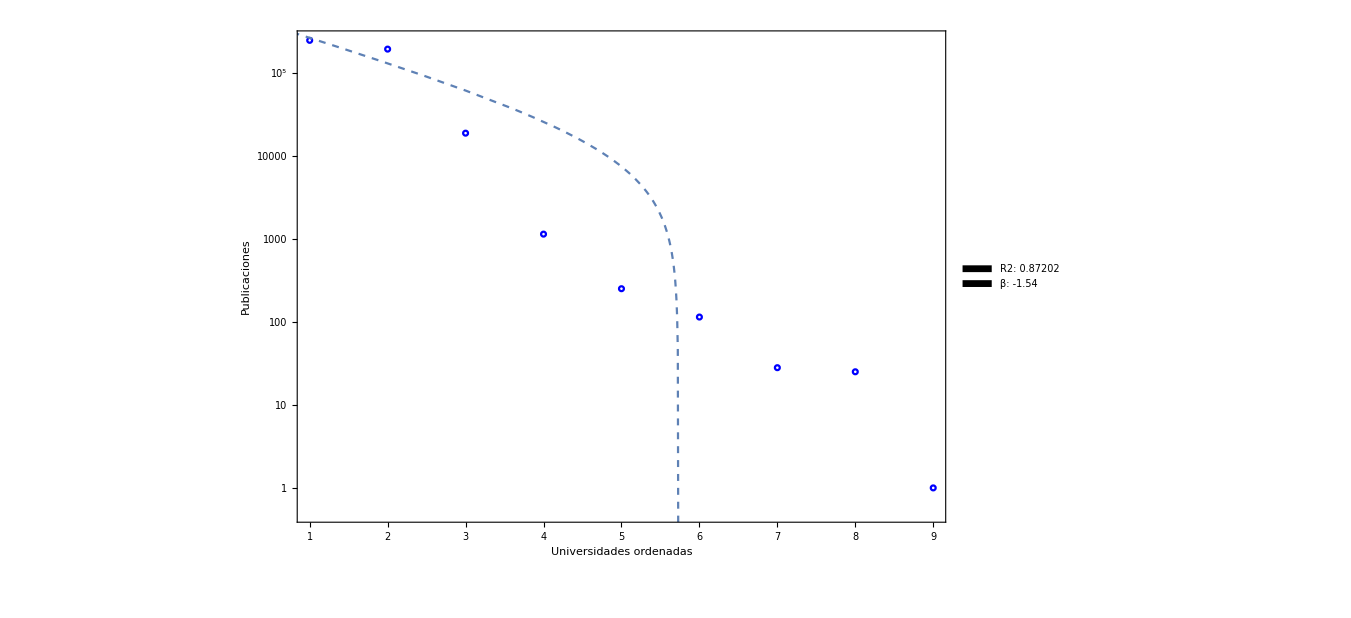

```mathematica
data2 = Import[y<>"/SinCompetencia/averageResults/dataUniversity-0.001-turtles.csv"];
Fdata2 = Flatten[data2];
lm1=NonlinearModelFit[Fdata2,(a) ^ (  (b x) + d )+ (c),{a,b, c, d},x]
P1=lm1[{"BestFit"}]
R21=lm1["AdjustedRSquared"] //ToString
Legended[Show[ListLogPlot[{Fdata2}, PlotRange->All, PlotStyle->{Blue},PlotMarkers->{Graphics[{Circle[]},ImageSize-> 5]}],LogPlot[lm1[x],{x,-19,8}, PlotStyle->{Dashed}], AxesLabel->{"Universidades ordenadas", "Publicaciones"},ImageSize->1000, Frame->True,FrameLabel->{Style["Universidades ordenadas",Black,Large],Style["Publicaciones",Black,Large]}],Placed[SwatchLegend[{Black,Black},{Style["R2: "<>R21,15],Style["β: -1.54",15]},LegendMargins->{{0,0},{0,0}},LabelStyle->(FontFamily->"Helvetica")],{{0.60,0.6},{0,0}}]]
```

FittedModel[-9343.37+1.6095^(27.6853-1.53658 x)]

{-9343.37+1.6095^(27.6853-1.53658 x)}

0.890678

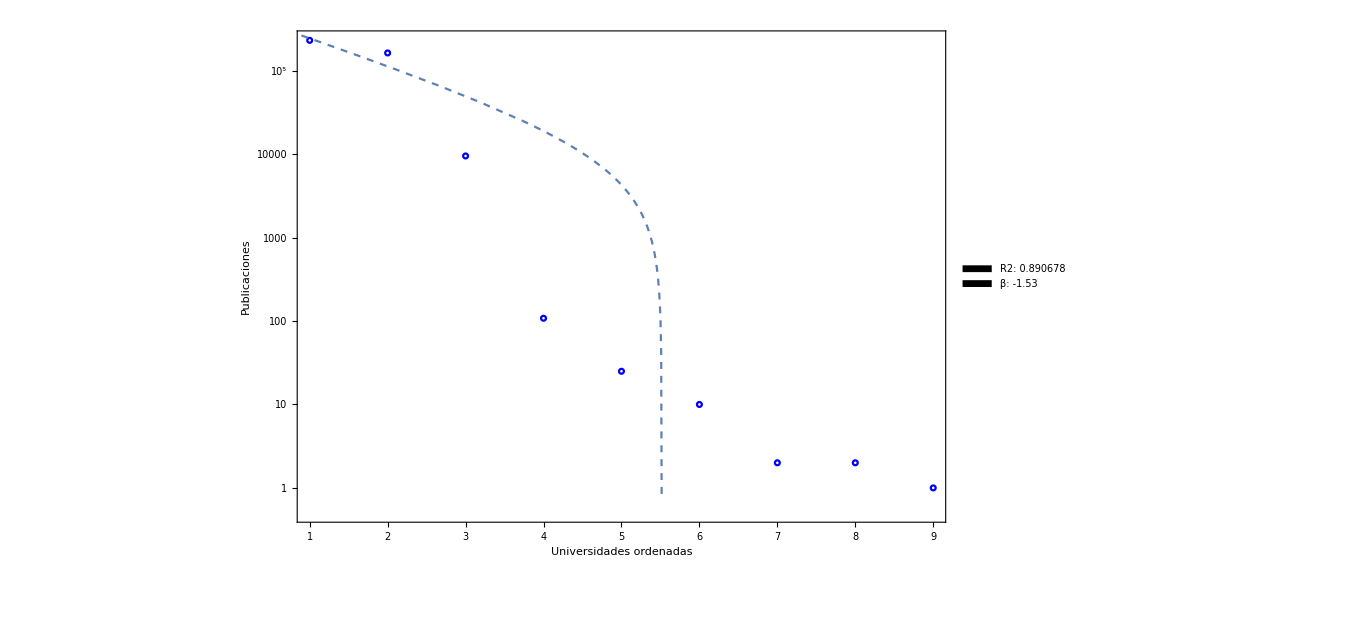

```mathematica
data2 = Import[y<>"/SinCompetencia/averageResults/dataUniversity-1.0E-4-turtles.csv"];
Fdata2 = Flatten[data2];
lm1=NonlinearModelFit[Fdata2,(a) ^ (  (b x) + d )+ (c),{a,b, c, d},x]
P1=lm1[{"BestFit"}]
R21=lm1["AdjustedRSquared"] //ToString
Legended[Show[ListLogPlot[{Fdata2}, PlotRange->All, PlotStyle->{Blue},PlotMarkers->{Graphics[{Circle[]},ImageSize-> 5]}],LogPlot[lm1[x],{x,-18,8}, PlotStyle->{Dashed}], AxesLabel->{"Universidades ordenadas", "Publicaciones"},ImageSize->1000, Frame->True,FrameLabel->{Style["Universidades ordenadas",Black,Large],Style["Publicaciones",Black,Large]}],Placed[SwatchLegend[{Black,Black},{Style["R2: "<>R21,15], Style["β: -1.53",15]},LegendMargins->{{0,0},{0,0}},LabelStyle->(FontFamily->"Helvetica")],{{0.60,0.6},{0,0}}]]
```

FittedModel[-272.478+1.79836^(21.3809-2.44048 x)]

{-272.478+1.79836^(21.3809-2.44048 x)}

0.998834

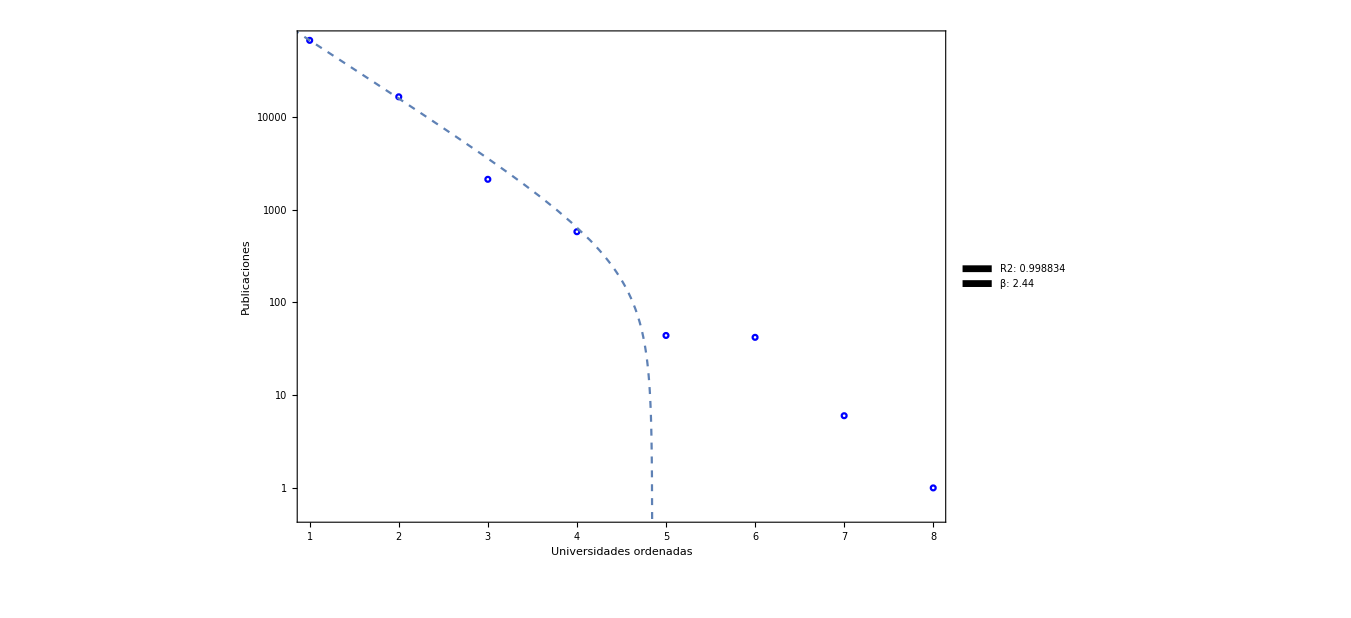

```mathematica
data2 = Import[y<>"/ConCompetencia/averageResults/dataUniversity-0.01-turtles.csv"];
Fdata2 = Flatten[data2];
lm1=NonlinearModelFit[Fdata2,(a) ^ (  (b x) + d )+ (c),{a,b, c, d},x]
P1=lm1[{"BestFit"}]
R21=lm1["AdjustedRSquared"] //ToString
Legended[Show[ListLogPlot[{Fdata2}, PlotRange->All, PlotStyle->{Blue},PlotMarkers->{Graphics[{Circle[]},ImageSize-> 5]}],LogPlot[lm1[x],{x,-1,8}, PlotStyle->{Dashed}], AxesLabel->{"Universidades ordenadas", "Publicaciones"},ImageSize->1000, Frame->True,FrameLabel->{Style["Universidades ordenadas",Black,Large],Style["Publicaciones",Black,Large]}],Placed[SwatchLegend[{Black,Black},{Style["R2: "<>R21,15], Style["β: 2.44",15]},LegendMargins->{{0,0},{0,0}},LabelStyle->(FontFamily->"Helvetica")],{{0.60,0.6},{0,0}}]]
```

FittedModel[14.6179+1.82342^(25.8235-7.42057 x)]

{14.6179+1.82342^(25.8235-7.42057 x)}

0.999999

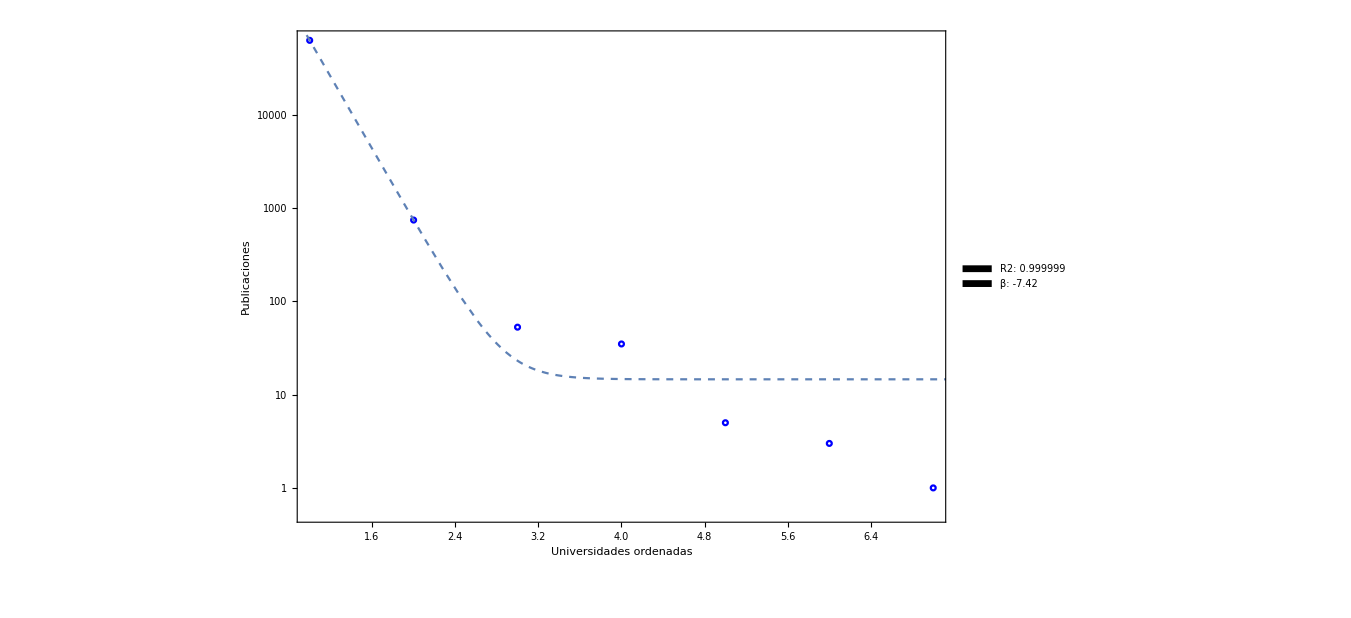

```mathematica
data2 = Import[y<>"/ConCompetencia/averageResults/dataUniversity-0.001-turtles.csv"];
Fdata2 = Flatten[data2];
lm1=NonlinearModelFit[Fdata2,(a) ^ (  (b x) + d )+ (c),{a,b, c, d},x]
P1=lm1[{"BestFit"}]
R21=lm1["AdjustedRSquared"] //ToString
Legended[Show[ListLogPlot[{Fdata2}, PlotRange->All, PlotStyle->{Blue},PlotMarkers->{Graphics[{Circle[]},ImageSize-> 5]}],LogPlot[lm1[x],{x,0,8}, PlotStyle->{Dashed}], AxesLabel->{"Universidades ordenadas", "Publicaciones"},ImageSize->1000, Frame->True,FrameLabel->{Style["Universidades ordenadas",Black,Large],Style["Publicaciones",Black,Large]}],Placed[SwatchLegend[{Black,Black},{Style["R2: "<>R21,15], Style["β: -7.42",15]},LegendMargins->{{0,0},{0,0}},LabelStyle->(FontFamily->"Helvetica")],{{0.60,0.6},{0,0}}]]
```

FittedModel[2.47997+1.98436^(25.9159-9.77417 x)]

{2.47997+1.98436^(25.9159-9.77417 x)}

1.

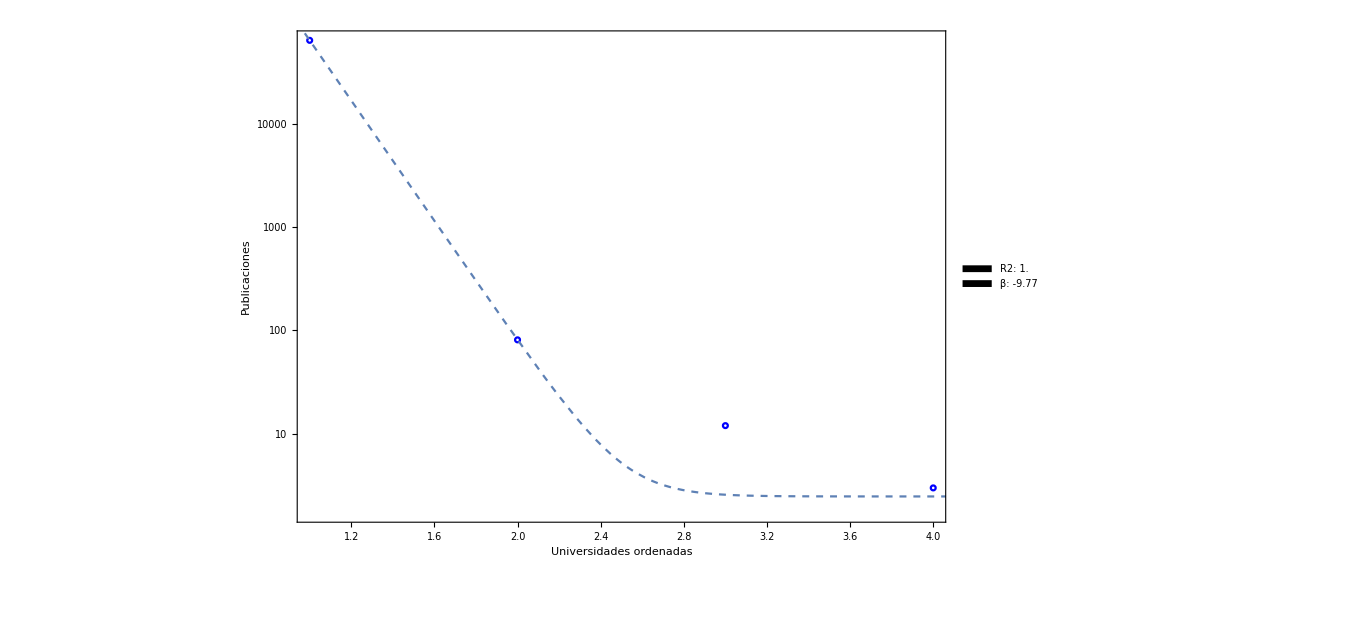

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados";
data2 = Import[y<>"/ConCompetencia/averageResults/dataUniversity-1.0E-4-turtles.csv"];
Fdata2 = Flatten[data2];
lm1=NonlinearModelFit[Fdata2,(a) ^ (  (b x) + d )+ (c),{a,b, c, d},x, AccuracyGoal->20,PrecisionGoal->6]
P1=lm1[{"BestFit"}]
R21=lm1["AdjustedRSquared"] //ToString
Legended[Show[ListLogPlot[{Fdata2}, PlotRange->All, PlotStyle->{Blue},PlotMarkers->{Graphics[{Circle[]},ImageSize-> 5]}],LogPlot[lm1[x],{x,0,8}, PlotStyle->{Dashed}], AxesLabel->{"Universidades ordenadas", "Publicaciones"},ImageSize->1000, Frame->True,FrameLabel->{Style["Universidades ordenadas",Black,Large],Style["Publicaciones",Black,Large]}],Placed[SwatchLegend[{Black,Black},{Style["R2: "<>R21,15],Style["β: -9.77",15]},LegendMargins->{{0,0},{0,0}},LabelStyle->(FontFamily->"Helvetica")],{{0.60,0.6},{0,0}}]]
```